```mathematica
Integrate[r^2 ⅇ^(-r/(x Sin[θ])),{r,rmin,rmax}]
```

x Sin[θ] (-ⅇ^(-(rmax Csc[θ])/x) (rmax^2+2 x Sin[θ] (rmax+x Sin[θ]))+ⅇ^(-(rmin Csc[θ])/x) (rmin^2+2 x Sin[θ] (rmin+x Sin[θ])))

```mathematica
Integrate[r^2/Sin[θ]^2 ⅇ^(-r/Sin[θ]),{r,0,∞},{θ,0,π}]
```

4

```mathematica
Integrate[r^2/Sin[θ]^2 ⅇ^(-r/(7Sin[θ])),{r,0,∞},{θ,0,π}]
```

1372

```mathematica
Integrate[r^2/Sin[θ]^2 ⅇ^(-r/(x Sin[θ])),{r,0,∞},{θ,0,π}]
```

ConditionalExpression[4 x^3,Re[x]>0&&Im[x]==0]

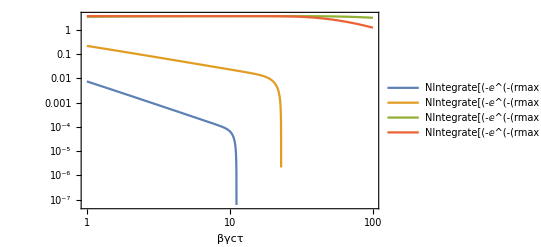

```mathematica
Block[{rmin=10^-4 500,rmax=162,θmin=17 Degree,θmax=150 Degree},LogLogPlot[{NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2))/(Sin[θ]^2 x^3),{θ,θmin,θmax}],NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 x Sin[θ] rmax)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] ( (2 x Sin[θ] rmin)))/(Sin[θ]^2 x^3),{θ,θmin,θmax}],NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2 ))/(Sin[θ]^2 x^3),{θ,θmin,θmax}],NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2+2 x Sin[θ] (rmax+x Sin[θ]))+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2+2 x Sin[θ] (rmin+x Sin[θ])))/(Sin[θ]^2 x^3),{θ,θmin,θmax}]},{x,1,100},Frame->True,PlotLegends->"Expressions",PlotRange->Full,FrameLabel->{"βγcτ",""}]]
```

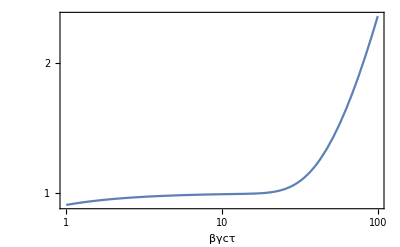

```mathematica
Block[{rmin=10^-4 500,rmax=162,θmin=17 Degree,θmax=150 Degree},LogLogPlot[{NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2 ))/(Sin[θ]^2 x^3),{θ,θmin,θmax}]/NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2+2 x Sin[θ] (rmax+x Sin[θ]))+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2+2 x Sin[θ] (rmin+x Sin[θ])))/(Sin[θ]^2 x^3),{θ,θmin,θmax}]},{x,1,100},Frame->True,PlotLegends->"Expressions",PlotRange->Full,FrameLabel->{"βγcτ",""}]]
```

General::munfl: Exp[-27123.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

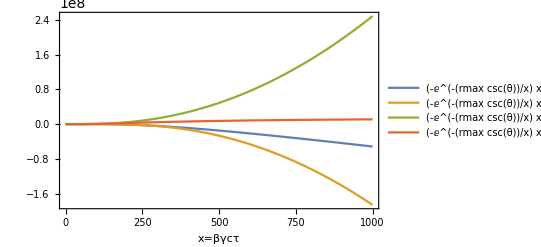

```mathematica
Block[{rmin=10^-4 500,rmax=162,θmin=17 Degree,θmax=150 Degree,θ=17 Degree},Plot[{(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 x Sin[θ] rmax)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] ( (2 x Sin[θ] rmin)))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2 ))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2+2 x Sin[θ] (rmax+x Sin[θ]))+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2+2 x Sin[θ] (rmin+x Sin[θ])))/Sin[θ]^2},{x,0,1000},Frame->True,PlotLegends->"Expressions",PlotRange->Full,FrameLabel->{"x=βγcτ",""}]]
```

General::munfl: Exp[-135616.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

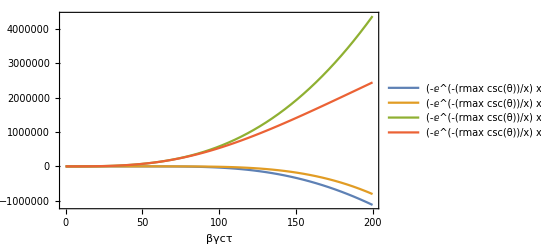

```mathematica
Block[{rmin=10^-4 500,rmax=162,θmin=17 Degree,θmax=150 Degree,θ=17 Degree},Plot[{(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 x Sin[θ] rmax)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] ( (2 x Sin[θ] rmin)))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2 ))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2+2 x Sin[θ] (rmax+x Sin[θ]))+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2+2 x Sin[θ] (rmin+x Sin[θ])))/Sin[θ]^2},{x,0,200},Frame->True,PlotLegends->"Expressions",PlotRange->Full,FrameLabel->{"βγcτ",""}]]
```

General::munfl: Exp[-7930.07] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

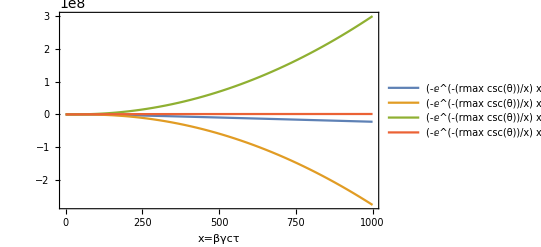

```mathematica
Block[{rmin=10^-4 500,rmax=162,θmin=17 Degree,θmax=150 Degree,θ=90 Degree},Plot[{(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 x Sin[θ] rmax)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] ( (2 x Sin[θ] rmin)))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2 ))/Sin[θ]^2,(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2+2 x Sin[θ] (rmax+x Sin[θ]))+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2+2 x Sin[θ] (rmin+x Sin[θ])))/Sin[θ]^2},{x,0,1000},Frame->True,PlotLegends->"Expressions",PlotRange->Full,FrameLabel->{"x=βγcτ",""}]]
```